# Vaje za 2. teden

7. 3. 2024

## Ponovitev

Izračunaj 1+x+x^2+x^3, kjer je x = 1/√e+1/√π, na dva načina: naprej s pomočjo prepisovalnega pravila, nato pa še tako, da definiraš vrednost spremenljivke x.
Spremenljivko x na koncu pobriši.

```mathematica
f[x_] := 1 + x + x^2 + x^3
f[1/E^0.5 + 1/Pi^0.5]
x = 1/E^0.5 + 1/Pi^0.5
f[x]
```

5.14588

1.17072

5.14588

## Naloga 1

Izračunaj 1000-i decimalki števil e in π na dva načina:
1. Tako da izračunaš dovolj decimalk obeh števil in pogledaš ustrezno decimalko pri koncu. Zakaj zadnja decimalka ne bo v redu? Uporabi funkcijo N tako, da ji podaš natančnost.
2. Z uporabo funkcije RealDigits in izpisom ustreznega elementa seznama.

Določi še 5., 100. in 443. decimalko.

Napiši fuknkcijo, ki sprejme poljubno realno število x in naravno število n in vrne n-to decimalko števila x.

## Naloga 2

V Matematico vnesi izraz sin(π/8)+cos(π/8). Kaj Mathematica vrne? Nato poskusi ta izraz poenostaviti s primernim izrazom (končni rezultat se “lepo” izrazi s koreni).Definiraj niz niz, ki bo lepo predstavil in zapisal rešitev te naloge. Po klicu spremenljivke niz naj tako Mathematica izpiše spodnji niz, kjer naj bo niz “___” nadomeščen s pravim rezultatom.
"Vsota sin(π/8) + cos(π/8) je enaka ___."

## Naloga 3

Napiši  funkcijo poenostaviInIzpisi, ki  bo  sprejela  izraz “izr”, ga  poenostavila  in  rezultat  izpisala  v  obliki
“Izraz [izr] se poenostavi v izraz [poenostavljen_izraz]”,
kjer je [izr] nadomestite z vnešenim izrazom, [poenostavljen_izraz] pa s poenostavljenim izrazom.

## Naloga 4

Matej ima 249 jabolk, Jana pa 419 jabolk. Koliko jabolk imata skupaj?
Rešitev zgornje naloge predstavi z nizom, ki ga shrani v spremenljivki niz. Ob klicu spremenljivke niz naj Mathematica vrne:
“Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.”
Pomagaj si z vodičem za generiranje nizov (predvsem del za vstavljanje izrazov) in uporabi funkcijo TemplateApply, da definiraš zgornji niz še brez direktnega vnašanja števila 668.

## Naloga 5

1. Definiraj funkcijo f(x)=x^2+3x+2+sin(x).
2. Izračunaj f(3)+f(4).  Uporabi tako prefiksni kot postfiksni način klica funkcije. Rezultat izpiši numerično (kot približek).
3. Nariši graf funkcije f na intervalu [-10,10].
4. Definiraj funkcijo g z istim predpisom kot f, pri čemer g definiraj kot anonimno funkcijo s formalnim parametrom #.
5. Definiraj funkcijo h(x,y)=(f(x)+g(y))^2 na dva načina: na standardni način in kot anonimno funkcijo.

## Naloga 6

1. Definiraj funkciji f(x) in g(n), kjer je f(x)=x^3+x+1, g(n) pa je ostanek števila n pri deljenju s 7.
2. Ustvari seznam {f(1),f(2),...,f(100)}. Poišči vsa števila n s tega seznama, za katere je g(n)=3. Uporabi ukaz Select.
3. Poskusi rešiti zgornjo nalogo v eni vrstici s pomočjo uporabe anonimnih funkcij.

## Naloga 7

Kaj vrne spodnja koda? Pojasni vsako vrstico!

```mathematica
VsotaKvadratov[x_,y_]:=x^2+y^2
AplicirajFunkcijo2Spremenljivk[f_,x_,y_]:=f[x,y]
AplicirajFunkcijo2Spremenljivk[VsotaKvadratov,3,4]
```

Zgornja koda vsebuje 3 vrstice. Zapiši ekvivalent te kode z uporabo anonimne funkcije, ki vsebuje le 1 vrstico.

## Naloga 8

Nariši graf funkcije f (x, y, z) = x  sin (xy)  cos (xy + z), kjer za z-koordinato uporabi  slider.

## Naloga 9

V pomoči si poglej ukaz Join. Definiraj seznam {1,2,...,100,1,2,...,100}. Definiraj še funkcijo DvojniSeznam[n], ki vrne dvojni seznam {1,2,...,n,1,2,...,n}.

Kaj dela spodnja funkcija?

```mathematica
Krogi[n_]:=Join[{Red},Table[Disk[{2i,0}],{i,n}]]
```

Definiraj funkcijo NarisiKroge[n], ki nariše n rdečih krogov. Barve lahko definiraš tudi drugače, uporabi domišljijo. Pomagaj si s funkcijo Graphics. Na primer, klic NarisiKroge[5] naj vrne nekaj takega kot:

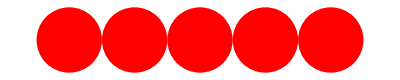

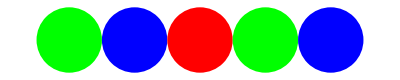
Za dodatni izziv poskusi napisati funkcijo MesaniKrogi[n], ki bo narisala kroge v izmenjajočih barvah. Na primer:
-Graphics-

Na podoben način definiraj še funkcijo NarisiKrogle[n], ki nariše n sfer. Sfere lahko postaviš tudi drugače (ne nujno v ravni vrsti).

Nariši interaktivni 3d graf, ki vsebuje tri zaporedne krogle, vsaki od katerih lahko spreminjaš njeno drugo koordinato.

-Graphics3D-

## Naloga 10

Napiši funkcijo, ki sprejme narvni števili m in n in vrne seznam prvih n členov Collatzovega zaporedja za število m. Pomagaj si s funkcijo “RecurrenceTable”.